Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1.  If z moves from z=1/4 twice around the circle Abs[z] = 1/4, what does w = √z do?

Using polar coordinates

```mathematica
z=r ⅇ^(ⅈ θ)
```

ⅇ^(ⅈ θ) r

Since I’m looking at the position r=1/4, I have

```mathematica
Subscript[z, 0]=1/4 ⅇ^(ⅈ θ)
```

ⅇ^(ⅈ θ)/4

As for the mapping considered, it is w=√z, so that

```mathematica
Subscript[w, 0]=(1/4 ⅇ^(ⅈ ϕ))^(1/2)
```

```mathematica
(√(ⅇ^(ⅈ ϕ)))/2==ⅇ^(ⅈ ϕ/2)/2
```

Analyzing, I see that in w-space the circle has twice the radius and half the angle. So going around twice on a 1/4-unit circle in z-space will transfer to the equivalent of going around once on a 1/2-unit circle in w-space.

3.  Make a sketch, similar to figure 395, of the Riemann surface of w = (z+1)^(1/4).

With a radical of 4th order, I would expect that many roots = sheets, according to statements on page 616 of text. And that is what the text answer says. However Mathematica will not specifically tell me what the roots are, not when using Solve, FindRoot, FindInstance, or Reduce. Actually, I see that the derivative is what I need to analyze critical points.

```mathematica
Clear["Global`*"]
```

```mathematica
f[z_]=(z+1)^(1/4)
```

(1+z)^(1/4)

```mathematica
D[f[z],z]
```

1/(4 (1+z)^(3/4))

```mathematica
Solve[1/(4 (1+z)^(3/4))==0,z]
```

{{z→ComplexInfinity}}

Although Mathematica doesn’t say so, I could assume that there are four multiple roots, each of complex infinity.

First I showcase an experimental function. The function below is a curiosity, contributed to MMAStackExchange question 3458 by celschk. The function fits both real and imaginary sheets onto a single compound sheet by use of absolute value function. The plot on the left is the result of calling the current problem function. The following comment was included in the answer, and refers to the sample plot on the right: “Positive real numbers are red, negative real numbers are cyan. One can e.g. see that the poles of the Gamma function are of order one because going round them you go through the colour cycle just once.” It’s an odd but interesting take on complex plotting, though I’ll reserve judgment as to whether it “...gives the complete information for a function, f :> ℂ↦ℂ.”

```mathematica
ComplexFnPlot[f_,range_,options___]:=Block[{rangerealvar,rangeimagvar,g},g[r_,i_]:=(f/.range[[1]]:>r+I i);
Plot3D[Abs@g[rangerealvar,rangeimagvar],{rangerealvar,Re@range[[2]],Re@range[[3]]},{rangeimagvar,Im@range[[2]],Im@range[[3]]},options,ColorFunction->(Hue@Mod[Arg@g[#1,#2]/(2*Pi)+1,1]&),ColorFunctionScaling->False]]
```

```mathematica
Row[{ComplexFnPlot[(z+1)^(1/4),{z,-4-4ⅈ,4+4ⅈ},PlotRange->{0,2},ImageSize->300,BoxRatios->{1, 1, 1}],ComplexFnPlot[Gamma[z],{z,-3.5-3.5I,3.5+5.5I},PlotRange->{0,4},ImageSize->300]}]
```

-Graphics3D--Graphics3D-

The following plot meets several requirements. Its appearance has something to recommend it. I don’t know enough about it to judge whether it is correct.

```mathematica
ParametricPlot3D[{{r Cos[θ],r Sin[θ],Im[(r ⅇ^(ⅈ θ)+1)^(1/4)]},{r Cos[θ],r Sin[θ],ⅈ Im[(r ⅇ^(ⅈ θ)+1)^(1/4)]},{r Cos[θ],r Sin[θ],-ⅈ Im[(r ⅇ^(ⅈ θ)+1)^(1/4)]},{r Cos[θ],r Sin[θ],- Im[(r ⅇ^(ⅈ θ)+1)^(1/4)]},{r Cos[θ],r Sin[θ],Re[(r ⅇ^(ⅈ θ)+1)^(1/4)]},{r Cos[θ],r Sin[θ],ⅈ Re[(r ⅇ^(ⅈ θ)+1)^(1/4)]},{r Cos[θ],r Sin[θ],-ⅈ Re[(r ⅇ^(ⅈ θ)+1)^(1/4)]},{r Cos[θ],r Sin[θ],- Re[(r ⅇ^(ⅈ θ)+1)^(1/4)]}},{r,0,5},{θ,0,2π},AxesLabel->{r,θ,v},ImageSize->200,BoxRatios->{1, 1, 1.1}]
```

-Graphics3D-

Another version of Riemann surface for this equation is inspired by an updated Michael Trott formula, seen at https://mathematica.stackexchange.com/questions/155850/on-visualizing-riemann-surfaces-of-algebraic-functions. It has considerable appeal, though it seems to lack a kind of helical continuity. It definitely shows four sheets.

```mathematica
With[{ε=1.*^-12},Show[Function[f,Plot3D[Re[f],{x,#1,#2},{y,#3,#4},BoundaryStyle->None,Mesh->False,PlotPoints->25,PlotStyle->Directive[Opacity[0.6,Hue[0.82]],Specularity[Hue[0.22],1.21]]]&@@@{{ε,2,ε,2},{-ε,-2,ε,2},{-ε,-2,-ε,-2},{ε,2,ε,-2}}]/@{Simplify[(x+1+ⅈ y)^(1/4)],-Simplify[(x+1+ⅈ y)^(1/4)],ⅈ Simplify[(x+1+ⅈ y)^(1/4)],-ⅈ Simplify[(x+1+ⅈ y)^(1/4)]},BoxRatios->{1.,1.,1.},PlotRange->All,ViewPoint->{4.,-2.,1.7}]]
```

-Graphics3D-

4 - 10 Riemann surfaces
Find the branch points and the number of sheets of the Riemann surface.

Note: In Mathematica 11 documentation, under Mathematical_Functions>Functions_that_do_not_have_a_unique_value, there is a explanaton/tutorial about branch cuts. This information is available also in the version of Wolfram Documentation on the web. I understand there is some variance in guidance about how to determine branch cuts.

5.  z^2+(4 z+ⅈ)^(1/3)

The order of the radical indicates there will be 3 sheets.

```mathematica
ComplexAnalysis`BranchCuts[z^2+(4 z+ⅈ)^(1/3),z];
Assuming[{x,y}∈Reals,Simplify[%/.z->x+I y]]
```

x<0&&y==-1/4

The above branchcut function, which may be the one that Mathematica uses when and if it finds the need for one, can be traced to https://community.wolfram.com/groups/-/m/t/866255.

7.  (z-z_0)^(1/n)

The order of the radical indicates there will be n sheets. The obvious branch cut is at z_0.

9.  √(z^3+z)

The below brown cells explore a Mathematica diversion which I don’t understand.

```mathematica
ComplexAnalysis`BranchCuts[√(z^3+z),z];
Assuming[{x,y}∈Reals,Simplify[%/.z->x+I y]]
```

(x<0&&y==0)||(x>0&&(√(1+3 x^2)+y==0||√(1+3 x^2)==y))

The below plot is in the complex plane.

```mathematica
p1=ParametricPlot[{Re[√((x+ⅈ y)^3+(x+ⅈ y))],Im[√((x+ⅈ y)^3+(x+ⅈ y))]},{x,-2,2},{y,-2,2}];
```

The two plots following are in the real plane. However, considering the way the complex plane is set up, I believe that superimposing them on the above plot is acceptable, though it does not seem to advance understanding.

```mathematica
p2=Plot[-√(1+3 x^2),{x,0,3},Exclusions->{x==0}];
```

```mathematica
p3=Plot[√(1+3 x^2),{x,0,3},Exclusions->{x==0}];
```

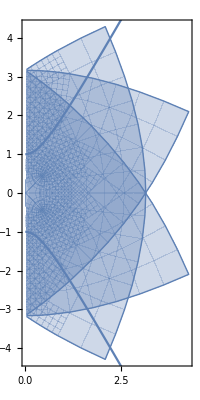

```mathematica
Show[p1,p2,p3]
```

Setting the above Mathematica digressions aside,  if y=0, there are three values of x which make the radical equal zero.

```mathematica
Solve[(x+ⅈ y)^3-(x+ⅈ y)==0&&{x,y} ∈ Reals]
```

{{x→-1,y→0},{x→0,y→0},{x→1,y→0}}

But looking at it from perspective of z, there are two other values, making five possibilities in total

```mathematica
Solve[√(z^3+z)==0,z]
```

{{z→0},{z→-ⅈ},{z→ⅈ}}

To advance five possible branch cuts when canonically there should only be three is probably very presumptous, but there it is.

I’ll end this section by looking at the problem function through the lens of the experimental complex plotting function introduced at the beginning of the section. The three points of discontinuity are clearly seen, at the points -1, 0, and 1, where they are expected. However, I don’t see in this case that the coloration helps determine their real or imaginary nature.

```mathematica
ComplexFnPlot[f_,range_,options___]:=Block[{rangerealvar,rangeimagvar,g},g[r_,i_]:=(f/.range[[1]]:>r+I i);
Plot3D[Abs@g[rangerealvar,rangeimagvar],{rangerealvar,Re@range[[2]],Re@range[[3]]},{rangeimagvar,Im@range[[2]],Im@range[[3]]},options,ColorFunction->(Hue@Mod[Arg@g[#1,#2]/(2*Pi)+1,1]&),ColorFunctionScaling->False]]
```

```mathematica
ComplexFnPlot[(z^3+z)^(1/2),{z,-4-4ⅈ,4+4ⅈ},PlotRange->{0,2},ImageSize->300,BoxRatios->{1, 1, 1},ViewPoint->{4000.,-2000.,1700}]
```

-Graphics3D-